# Кинематический расчет механизма векторным методом

Имеем следующий механизм:-Graphics-

Произвести кинематический расчет

Дано:

(Если хочешь посмотреть на анимацию снизу, то вот вот в этой ячейке снизу нужно поставить курсор куда нибудь и нажать Shift+ Enter (это запускает вычисление ячейки), всплывет окно, в нём нажать да и всё)

```mathematica
AB:= 0.1
BC:=0.3
H:=0.32 
ϕ100:=Pi/4
ω:=15
ϵ:=15
```

Обозначим звенья:
AB - ā
BC - b̄
BD - c̄
Углы:
ϕ_10 - угол поворота локальной СК№1 в базовую СК
ϕ_21 - угол поворота локальной СК№2 в локальную СК№1

Проведем геометрический анализ механизма, из которого получим зависимость угла ϕ_21 от ϕ_10

Воспользовавшись теоремой косинусов:

```mathematica
Solve[(AB*Cos[f10]+BC*Cos[ArcSin[AB/BC Sin[f10]]])^2== AB^2+BC^2+2*AB*BC*Cos[f21],f21]
```

Получаем функцию ϕ21= f(ϕ10):

```mathematica
f[x_/;Sin[x]≥ 0]:=2Pi*IntegerPart[x/(2Pi)]+ArcCos[1/(2*AB*BC)((AB^2 Cos[x]^2-AB^2 Sin[x]^2-AB^2)+2*AB*BC*Cos[x]*√(1-AB^2 Sin[x]^2/BC^2))]
f[x_/;Sin[x]<  0]:=2Pi*IntegerPart[x/(2Pi)]+2Pi-ArcCos[1/(2*AB*BC)((AB^2 Cos[x]^2-AB^2 Sin[x]^2-AB^2)+2*AB*BC*Cos[x]*√(1-AB^2 Sin[x]^2/BC^2))]
```

Посмотрим наглядно как зависит угол ϕ_21 от ϕ_10

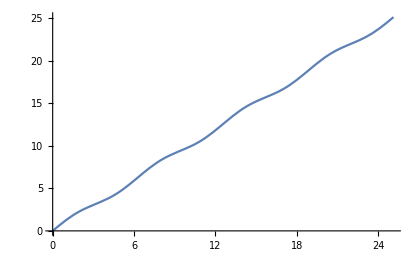

```mathematica
Plot[f[x],{x,0,8Pi},PlotRange->{0,8Pi}]
```

Радиус вектор любой точки (A,B,C,D) можно определить как сумму векторов ā,b̄,c̄

В своей локальной СК вектора ā,b̄,c̄ будут иметь вид вектора столбца:

```mathematica
a:={AB,0,0}
b:={BC,0,0}
s:={BC/2,0,0}
```

```mathematica
MatrixForm[a]
MatrixForm[b]
```

```mathematica
a=({{0.1}, {0}, {0}})
```

```mathematica
b=({{0.3}, {0}, {0}})
```

Причем вектор c̄ будет иметь непостоянную длину, она зависит от угла ϕ_10.
Выразим вектор c̄ изучая геометрию механизма. Получим:

```mathematica
c[x_]:={0,(H-AB*Sin[ϕ10])/Cos[f[ϕ10]-ϕ10],0}/.ϕ10->x
```

```mathematica
MatrixForm[c[ϕ]]
```

(0
Sec[ϕ-f[ϕ]] (0.32-0.1 Sin[ϕ])
0)

Определим радиус вектора точек B,C:

```mathematica
Rb[x_]:=M10[x].a
Rc[x_]:=M10[x].a+M20[x].b
Rs2[x_]:=M10[x].a+M20[x].s
```

Где М_10 и М_20 матрицы поворота.
Определим их как:

```mathematica
M10[x_]:={{Cos[x],-Sin[x],0},{Sin[x],Cos[x],0},{0,0,1}}
M21[x_]:={{Cos[f[x]],Sin[f[x]],0},{-Sin[f[x]],Cos[f[x]],0},{0,0,1}}
M20[x_]:=M21[x].M10[x]
```

```mathematica
MatrixForm[M10[ϕ]]
MatrixForm[M20[ϕ]]
```

(Cos[ϕ] | -Sin[ϕ] | 0
Sin[ϕ] | Cos[ϕ] | 0
0 | 0 | 1)

(Cos[ϕ] Cos[f[ϕ]]+Sin[ϕ] Sin[f[ϕ]] | -Cos[f[ϕ]] Sin[ϕ]+Cos[ϕ] Sin[f[ϕ]] | 0
Cos[f[ϕ]] Sin[ϕ]-Cos[ϕ] Sin[f[ϕ]] | Cos[ϕ] Cos[f[ϕ]]+Sin[ϕ] Sin[f[ϕ]] | 0
0 | 0 | 1)

Посмотрим графики проекций координат точки С на оси Х и У:

```mathematica
MatrixForm[Rc[ϕ]]
```

(0.1 Cos[ϕ]+0.3 (Cos[ϕ] Cos[f[ϕ]]+Sin[ϕ] Sin[f[ϕ]])
0.1 Sin[ϕ]+0.3 (Cos[f[ϕ]] Sin[ϕ]-Cos[ϕ] Sin[f[ϕ]])
0.)

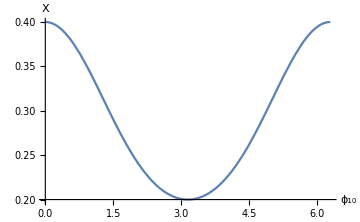
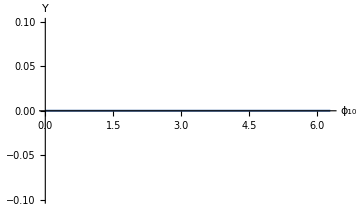

```mathematica
Row[ {Plot[0.1 Cos[ϕ]+0.3 (Cos[ϕ] Cos[f[ϕ]]+Sin[ϕ] Sin[f[ϕ]]),{ϕ,0,2Pi},ImageSize->Medium,AxesLabel->{Subscript[ϕ, 10],X}],Plot[0.1 Sin[ϕ]+0.3 (Cos[f[ϕ]] Sin[ϕ]-Cos[ϕ] Sin[f[ϕ]]),{ϕ,0,2Pi},PlotRange->{-0.1,0.1},AxesLabel->{Subscript[ϕ, 10],Y},ImageSize->Medium]}]
```

Как мы видим У-координата точки С остается постоянной, Х-координата совершает колебания с амплитудой 0.1.

Теперь изучим движение точки D. Радиус вектор точки D:

```mathematica
Rd[x_]:=M10[x].a+M20[x].c[x]
```

```mathematica
MatrixForm[Rd[ϕ]]
```

(0.1 Cos[ϕ]+Sec[ϕ-f[ϕ]] (0.32-0.1 Sin[ϕ]) (-Cos[f[ϕ]] Sin[ϕ]+Cos[ϕ] Sin[f[ϕ]])
0.1 Sin[ϕ]+Sec[ϕ-f[ϕ]] (0.32-0.1 Sin[ϕ]) (Cos[ϕ] Cos[f[ϕ]]+Sin[ϕ] Sin[f[ϕ]])
0.)

Построим графики проекций координат точки D на оси Х и У:

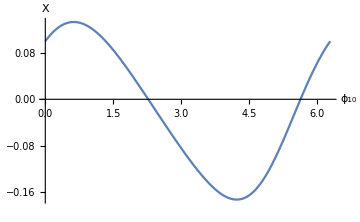
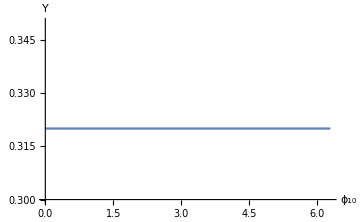

```mathematica
Row[ {Plot[0.1 Cos[ϕ]+Sec[ϕ-f[ϕ]] (0.32-0.1 Sin[ϕ]) (-Cos[f[ϕ]] Sin[ϕ]+Cos[ϕ] Sin[f[ϕ]]),{ϕ,0,2Pi},ImageSize->Medium,AxesLabel->{Subscript[ϕ, 10],X}],Plot[0.1 Sin[ϕ]+Sec[ϕ-f[ϕ]] (0.32-0.1 Sin[ϕ]) (Cos[ϕ] Cos[f[ϕ]]+Sin[ϕ] Sin[f[ϕ]]),{ϕ,0,2Pi},PlotRange->{0.3,0.35},AxesLabel->{Subscript[ϕ, 10],Y},ImageSize->Medium]}]
```

Абсолютно такой же можно сделать вывод о движении точки D: Y-координата постоянна, Х-координата колеблется 
Также можно выбрать точку E которая в начальный момент времени совпадает с точкой D:

```mathematica
e[x_]:={0,(H-AB*Sin[x])/Cos[f[x]-x],0}
Ree[x_,y_]:=M10[x].a+M20[x].e[y]
```

```mathematica
MatrixForm[Ree[ϕ,Pi/4]]
```

(0.1 Cos[ϕ]+0.256517 (-Cos[f[ϕ]] Sin[ϕ]+Cos[ϕ] Sin[f[ϕ]])
0.1 Sin[ϕ]+0.256517 (Cos[ϕ] Cos[f[ϕ]]+Sin[ϕ] Sin[f[ϕ]])
0.)

Проанализировав изменение координат в зависимости от угла ϕ_10 можем изобразить схему всего механизма в завимости от угла ϕ_10

```mathematica
m=Animate[
ϕ1:=ϕ100+ω*t;
pA:={0,0};
pB:=Rb[ϕ1][[1;;2]];
pC:=Rc[ϕ1][[1;;2]];
pD:=Rd[ϕ1][[1;;2]];
pE:=Ree[ϕ1,ϕ100][[1;;2]];
pS2:=Rs2[ϕ1][[1;;2]];
Graphics[{Line[{pA,pB}],Line[{pB,pC}],HalfLine[{pB,pD}],Point[pS2],

Circle[#,0.005]&/@{pA,pB,pC,pD},Point[pE],Line[{{#[[1]]-0.025,#[[2]]-0.0125},{#[[1]]-0.025,#[[2]]+0.0125},{#[[1]]+0.025,#[[2]]+0.0125},{#[[1]]+0.025,#[[2]]-0.0125},{#[[1]]-0.025,#[[2]]-0.0125}}]&/@{pC,pD},
FontSize->14,Text[#[[1]],#[[2]] -0.02]&/@{ {"A",pA}, {"B",pB}, {"C",pC},{"E",pE},{"S2",pS2},{"D",pD}}


},
Axes->False,PlotRange->{{-0.2,0.4},{-0.2,0.4}}],{t,0,1}]
```

```mathematica
Df[y_/;Sin[y]≥0]:=D[ArcCos[1/(2*AB*BC)((AB^2 Cos[x]^2-AB^2 Sin[x]^2-AB^2)+2*AB*BC*Cos[x]*√(1-AB^2 Sin[x]^2/BC^2))],x]/.x->y
Df[y_/;Sin[y]<0]:=-D[ArcCos[1/(2*AB*BC)((AB^2 Cos[x]^2-AB^2 Sin[x]^2-AB^2)+2*AB*BC*Cos[x]*√(1-AB^2 Sin[x]^2/BC^2))],x]/.x->y
DDf[y_/;Sin[y]≥0]:=D[D[ArcCos[1/(2*AB*BC)((AB^2 Cos[x]^2-AB^2 Sin[x]^2-AB^2)+2*AB*BC*Cos[x]*√(1-AB^2 Sin[x]^2/BC^2))],x],x]/.x->y
DDf[y_/;Sin[y]<0]:=D[-D[ArcCos[1/(2*AB*BC)((AB^2 Cos[x]^2-AB^2 Sin[x]^2-AB^2)+2*AB*BC*Cos[x]*√(1-AB^2 Sin[x]^2/BC^2))],x],x]/.x->y
```

```mathematica
Vd[x_]:=ω{D[Rd[y][[1]],y]/.f'[y]->Df[y],D[Rd[y][[2]],y]/.f'[y]->Df[y]}/.y->x
Vc[x_]:=ω{D[Rc[y][[1]],y]/.f'[y]->Df[y],D[Rc[y][[2]],y]/.f'[y]->Df[y]}/.y->x
Vb[x_]:=ω{D[Rb[y][[1]],y]/.f'[y]->Df[y],D[Rb[y][[2]],y]/.f'[y]->Df[y]}/.y->x
Ve[x_,g_]:=ω{D[Ree[y,g][[1]],y]/.f'[y]->Df[y],D[Ree[y,g][[2]],y]/.f'[y]->Df[y]}/.y->x
Vs2[x_]:=ω{D[Rs2[y][[1]],y]/.f'[y]->Df[y],D[Rs2[y][[2]],y]/.f'[y]->Df[y]}/.y->x
```

```mathematica
Manipulate[Graphics[{Text["V_B",Vb[x]+0.1Vb[x]],Text["V_C",Vc[x]+0.2],Text["V_D",Vd[x]+0.2],Text["V_E",Ve[x,x]+0.1Ve[x,x]],Text["V_S2",Vs2[x]+0.1Vs2[x]], , Arrow[{{0,0},#}]&/@{Vb[x],Vc[x],Vd[x],Ve[x,x],Vs2[x]}},Axes->True,PlotRange->{{-3,3},{-3,3}}],{{x,ϕ100},0,2Pi}]
```

```mathematica
Subscript[a, D][x_]:=ω Re@{D[Vd[y][[1]],y]/.f'[y]->Df[y]/.Df'[y]->DDf[y],D[Vd[y][[2]],y]/.f'[y]->Df[y]/.Df'[y]->DDf[y]}/.y->x
Subscript[a, C][x_]:=ω Re@{D[Vc[y][[1]],y]/.f'[y]->Df[y]/.Df'[y]->DDf[y],D[Vc[y][[2]],y]/.f'[y]->Df[y]/.Df'[y]->DDf[y]}/.y->x
Subscript[a, B][x_]:=ω Re@{D[Vb[y][[1]],y]/.f'[y]->Df[y]/.Df'[y]->DDf[y],D[Vb[y][[2]],y]/.f'[y]->Df[y]/.Df'[y]->DDf[y]}/.y->x
Subscript[a, E][x_]:=ω Re@{D[Ve[y,x][[1]],y]/.f'[y]->Df[y]/.Df'[y]->DDf[y],D[Ve[y,x][[2]],y]/.f'[y]->Df[y]/.Df'[y]->DDf[y]}/.y->x
Subscript[a, S2][x_]:=ω Re@{D[Vs2[y][[1]],y]/.f'[y]->Df[y]/.Df'[y]->DDf[y],D[Vs2[y][[2]],y]/.f'[y]->Df[y]/.Df'[y]->DDf[y]}/.y->x
```

```mathematica
Manipulate[Graphics[{Text["a_B",Subscript[a, B][x]+0.1 Subscript[a, B][x]],Text["a_C",Subscript[a, C][x]+0.2],Text["a_D",Subscript[a, D][x]+0.2],Text["a_E",Subscript[a, E][x]+0.1 Subscript[a, E][x]],Text["a_S2",Subscript[a, S2][x]+0.1 Subscript[a, S2][x]], , Arrow[{{0,0},#}]&/@{Subscript[a, B][x],Subscript[a, C][x],Subscript[a, D][x],Subscript[a, E][x],Subscript[a, S2][x]}},Axes->True,PlotRange->{{-35,35},{-35,35}}],{x,0,2Pi}]
```